## Contour plot for the triaxial rotor

## 2-axis quantization: ℐ_2- maximal M.O.I

### Computing the contour plot for the triaxial nucleus when the second axis has the largest moment of inertia. The parameters must correspond to positive inertial factor A and positive k number.

```mathematica
(*Expression of the Hamiltonian - classical energy function*)
```

## Functions

```mathematica
j1[j_,θ_]:=j*Cos[θ];
j2[j_,θ_]:=j*Sin[θ];
Afct[I_,a1_,a2_,j_,θ_]:=a2*(1-j2[j,θ]/I)-a1;
ufct[I_,a1_,a2_,a3_,j_,θ_]:=(a3-a1)/Afct[I,a1,a2,j,θ];
v0fct[I_,a1_,a2_,j_,θ_]:=-(a1*j1[j,θ])/Afct[I,a1,a2,j,θ];
kfct[I_,a1_,a2_,a3_,j_,θ_]:=Sqrt[ufct[I,a1,a2,a3,j,θ]];
IF[moi_]:=1/(2*moi);
```

## Energy Function

```mathematica
Hen[I_,a1_,a2_,a3_,j_,theta_,θ_,ϕ_]:=I^2(1-Sin[θ]^2)(1-ufct[I,a1,a2,a3,j,theta]*Cos[ϕ]^2-v0fct[I,a1,a2,j,theta]/I Sin[ϕ])+ufct[I,a1,a2,a3,j,theta]*I^2*Cos[ϕ]^2+2v0fct[I,a1,a2,j,theta]*I*Sin[ϕ];
contour[I_,i1_,i2_,i3_,j_,theta_]:=Show[ContourPlot[Hen[I,IF[i1],IF[i2],IF[i3],j,theta*π/180,θ,ϕ],{θ,0,π},{ϕ,0,2π}]];
```

### Draft example

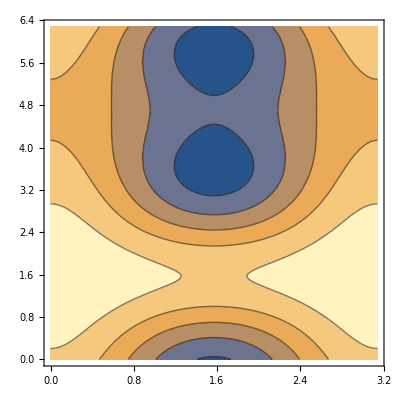

```mathematica
contour[19/2,35,40,20,j13,60]
```

### Other examples

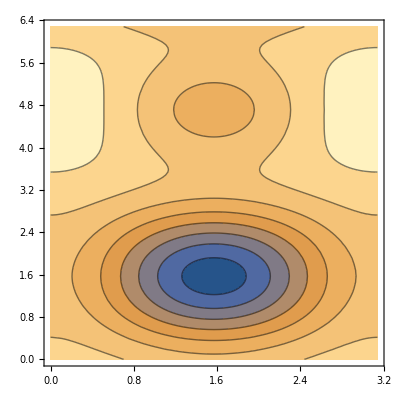

```mathematica
contour[19/2,85,100,65,j13,-80]
```

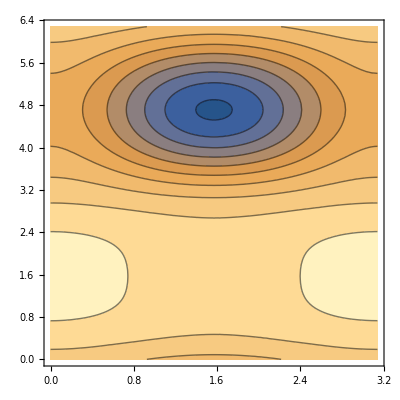

```mathematica
contour[19/2,10,60,30,j13,40]
```